```mathematica
(*Module[{data,dataH,gData},
data=Import["C:\\Users\\Alcatraz\\Documents\\cudaText.csv"];
{dataH,data}=(#@data&/@{First,Rest});
gData=GroupBy[data,#[[1]]&];
ListLinePlot[{#,Total[gData[#][[;;,3]]//Rest]}&/@Keys[gData],ImageSize->1200,Frame->True,PlotRange->All]

]*)
```

{{1,39},{39,25},{25,25},{25,34},{34,20},{20,38},{38,9},{9,15},{15,13},{13,39},{39,33},{33,40},{40,46},{46,30},{30,38},{38,40},{40,5},{5,34},{34,10},{10,24},{24,42},{42,36},{36,41},{41,1},{1,46},{46,30},{30,46},{46,29},{29,31},{31,30},{30,45},{45,38},{38,24},{24,45},{45,7},{7,28},{28,48},{48,44},{44,48},{48,40},{40,16},{16,46},{46,5},{5,3},{3,2},{2,43},{43,18},{18,18},{18,2},{2,45},{45,9},{9,25}}

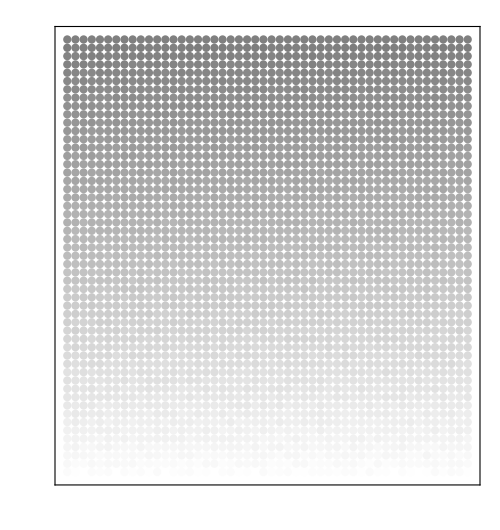

```mathematica
ClearAll[DiskPlotter];
DiskPlotter[list_?ListQ,yPosition_?NumberQ]:=MapThread[{GrayLevel@#1,Disk[{#2(*+RandomReal[{-0.1,0.1}]*),yPosition},0.5]}&,{list,Range[Length@list]}];

Module[{size=50,iterations,mins},
iterations=NestWhileList[Table[Clip[Max[#]+rand,{0,1}],{rand,RandomReal[{-0.01,0.01},size]}]&,ConstantArray[0.5,size],Max@#<1&];

mins=(Join@@Position[#,Min@#])[[1]]&/@iterations;
mins=Partition[Riffle[mins[[;;-2]],mins[[2;;]]],2];

Print@mins;

Graphics[
{
MapThread[DiskPlotter[#1,#2]&,{iterations,-Range@Length@iterations}](*,
MapThread[{Arrowheads@0.01,Arrow[{{#1[[1]],#2},{#1[[2]],#2-1}}]}&,{mins,-Range@Length@mins}]*)
}
,ImageSize->500,Frame->True,FrameTicks->False]
]
```